```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
```

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

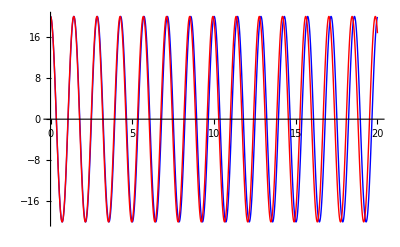

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

```mathematica
th = 50*π/180;
vt = 100;
ode2 = {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==30*Cos[ 50*π/180],y[0]== 2,y'[0]== 30*Sin[ 50*π/180]}
```

{x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,x'[0]==30 Sin[(2 π)/9],y[0]==2,y'[0]==30 Cos[(2 π)/9]}

```mathematica
sol = NDSolve[ode2,{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

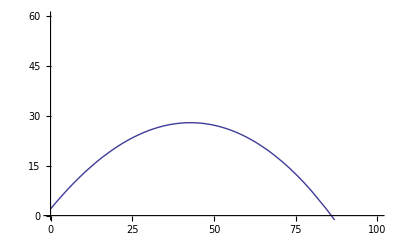

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotRange->{{0,100},{0,60}}]
```

```mathematica
Manipulate[
g=9.8;
ode2 ={x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==30*Cos[ 50*π/180],y[0]== 2,y'[0]== 30*Sin[ 50*π/180]};
sol = NDSolve[ode2,{x,y},{t,0,200}];
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}(*{V,0,Vf}*),PlotStyle-> {{Red},{Blue}},PlotRange-> All,AxesLabel->{"distance (m)","height (m)"},ImageSize->{500,300}],
{{tf,0.01,"time (s)"},0.01,100,Appearance->"Labeled"},{{V,30,"Initial Velocity (m/s)"},0.01,vt,Appearance->"Labeled"},{{vt,35,"Terminal Velocity (m/s)"},0.01,100,Appearance->"Labeled"}]
```